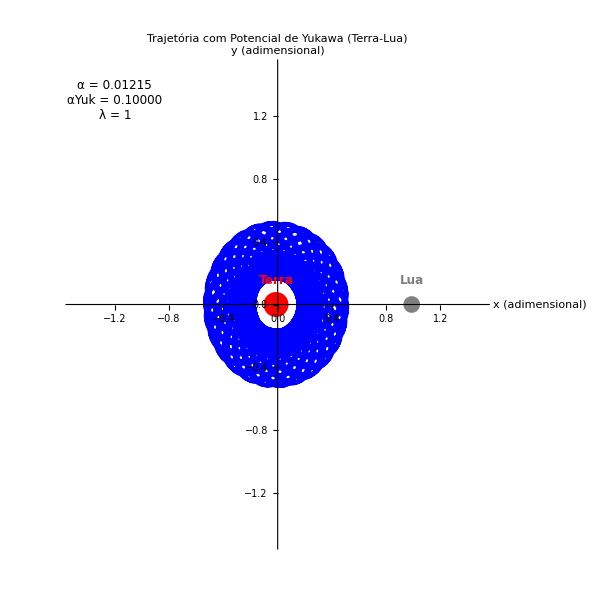

```mathematica
(*Parâmetros do Sistema*)EarthMass=5.97219*10^24;   (*Massa da Terra (kg)*)
MoonMass=7.34767309*10^22;  (*Massa da Lua (kg)*)
alphaMass=MoonMass/(EarthMass+MoonMass); (*Fração de massa da Lua*)
alphaYuk=0.1; (*Parâmetro de Yukawa*)
lambda=1; (*Alcance adimensional do potencial de Yukawa*)

(*Distâncias adimensionais*)
d1[x_,y_]:=Sqrt[(x+alphaMass)^2+y^2]; (*Distância à Terra*)
d2[x_,y_]:=Sqrt[(x-(1-alphaMass))^2+y^2]; (*Distância à Lua*)

(*Termos de Yukawa*)
q1[x_,y_]:=1+alphaYuk*Exp[-lambda*d1[x,y]];
q2[x_,y_]:=1+alphaYuk*Exp[-lambda*d2[x,y]];

(*Fator de correção k*)
k=1+alphaYuk*(1+lambda)*Exp[-lambda];

(*Potencial efetivo com Yukawa*)
UYukawa[x_,y_]:=-((1-alphaMass)/d1[x,y])*q1[x,y]-(alphaMass/d2[x,y])*q2[x,y]-(1/2)*(x^2+y^2);

(*Equações do Movimento modificadas*)
eq1Yuk=x''[t]==-D[UYukawa[x[t],y[t]],x[t]]+2*y'[t];
eq2Yuk=y''[t]==-D[UYukawa[x[t],y[t]],y[t]]-2*x'[t];

(*Condições Iniciais-mantidas iguais*)
x0=0.5;   (*Posição inicial em x*)
y0=0.1;   (*Posição inicial em y*)
vx0=0.0;  (*Velocidade inicial em x*)
vy0=0.5;  (*Velocidade inicial em y*)

(*Solução Numérica*)
solYuk=NDSolve[{eq1Yuk,eq2Yuk,x[0]==x0,y[0]==y0,x'[0]==vx0,y'[0]==vy0},{x,y},{t,0,100},Method->"StiffnessSwitching",MaxSteps->100000];

(*Plot comparativo*)
trajectoryPlotYuk=ParametricPlot[Evaluate[{x[t],y[t]}/. solYuk],{t,0,100},PlotStyle->{Blue,Thickness[0.005]},PlotRange->{{-1.5,1.5},{-1.5,1.5}},AxesLabel->{"x (adimensional)","y (adimensional)"},LabelStyle->{FontFamily->"Times New Roman",FontSize->14},PlotLabel->Style["Trajetória com Potencial de Yukawa (Terra-Lua)",14,Bold],ImageSize->600,Epilog->{{Red,PointSize[0.03],Point[{-alphaMass,0}],Text[Style["Terra",12,Bold],{-alphaMass,0.15}]},{Gray,PointSize[0.02],Point[{1-alphaMass,0}],Text[Style["Lua",12,Bold],{1-alphaMass,0.15}]},Text[Style[StringForm["α = ``\nαYuk = ``\nλ = ``",NumberForm[alphaMass,{4,5}],NumberForm[alphaYuk,{4,5}],NumberForm[lambda,{4,5}]],12],{-1.2,1.3},Background->White]}];

(*Exibir o gráfico*)
Print[trajectoryPlotYuk];
```

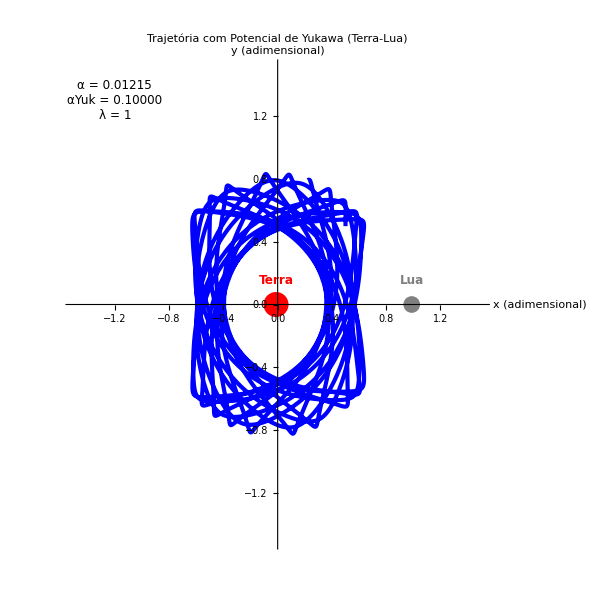

```mathematica
(*Parâmetros do Sistema*)EarthMass=5.97219*10^24;   (*Massa da Terra (kg)*)
MoonMass=7.34767309*10^22;  (*Massa da Lua (kg)*)
alphaMass=MoonMass/(EarthMass+MoonMass); (*Fração de massa da Lua*)
alphaYuk=0.1; (*Parâmetro de Yukawa*)
lambda=1; (*Alcance adimensional do potencial de Yukawa*)

(*Distâncias adimensionais*)
d1[x_,y_]:=Sqrt[(x+alphaMass)^2+y^2]; (*Distância à Terra*)
d2[x_,y_]:=Sqrt[(x-(1-alphaMass))^2+y^2]; (*Distância à Lua*)

(*Termos de Yukawa*)
q1[x_,y_]:=1+alphaYuk*Exp[-lambda*d1[x,y]];
q2[x_,y_]:=1+alphaYuk*Exp[-lambda*d2[x,y]];

(*Fator de correção k*)
k=1+alphaYuk*(1+lambda)*Exp[-lambda];

(*Potencial efetivo com Yukawa*)
UYukawa[x_,y_]:=-((1-alphaMass)/d1[x,y])*q1[x,y]-(alphaMass/d2[x,y])*q2[x,y]-(1/2)*(x^2+y^2);

(*Equações do Movimento modificadas*)
eq1Yuk=x''[t]==-D[UYukawa[x[t],y[t]],x[t]]+2*y'[t];
eq2Yuk=y''[t]==-D[UYukawa[x[t],y[t]],y[t]]-2*x'[t];

(*Condições Iniciais*)
x0=0.5;   (*Posição inicial em x*)
y0=0.5;   (*Posição inicial em y*)
vx0=0.0;  (*Velocidade inicial em x*)
vy0=0.5;  (*Velocidade inicial em y*)

(*Solução Numérica*)
solYuk=NDSolve[{eq1Yuk,eq2Yuk,x[0]==x0,y[0]==y0,x'[0]==vx0,y'[0]==vy0},{x,y},{t,0,100},Method->"StiffnessSwitching",MaxSteps->100000];

(*Plot comparativo*)
trajectoryPlotYuk=ParametricPlot[Evaluate[{x[t],y[t]}/. solYuk],{t,0,100},PlotStyle->{Blue,Thickness[0.005]},PlotRange->{{-1.5,1.5},{-1.5,1.5}},AxesLabel->{"x (adimensional)","y (adimensional)"},LabelStyle->{FontFamily->"Times New Roman",FontSize->14},PlotLabel->Style["Trajetória com Potencial de Yukawa (Terra-Lua)",14,Bold],ImageSize->600,Epilog->{{Red,PointSize[0.03],Point[{-alphaMass,0}],Text[Style["Terra",12,Bold],{-alphaMass,0.15}]},{Gray,PointSize[0.02],Point[{1-alphaMass,0}],Text[Style["Lua",12,Bold],{1-alphaMass,0.15}]},Text[Style[StringForm["α = ``\nαYuk = ``\nλ = ``",NumberForm[alphaMass,{4,5}],NumberForm[alphaYuk,{4,5}],NumberForm[lambda,{4,5}]],12],{-1.2,1.3},Background->White]}];

(*Exibir o gráfico*)
Print[trajectoryPlotYuk];
```